```mathematica
allGraphs5NullAtomKeys//Max
```

59048

```mathematica
ShowGraph5Least[59048]
```

-Graphics-590481

```mathematica
Table[allGraphs5[k,"chrom4"]=ChromaticPolynomial[allGraphs5[k,"graph"],4],{k,Keys[allGraphs5]}];
```

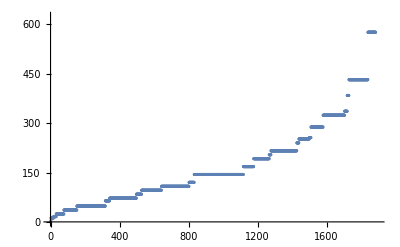

```mathematica
Table[allGraphs5[k,"chrom4"],{k,Sort[Keys[allGraphs5]]}]//Sort//N//ListPlot
```

```mathematica
g=MobiusGraph5[K5Key,allGraphs5];
```

```mathematica
Select[Sort[VertexList[g],CompareSymbols],StringCount[SymbolName[#],"x"]==2&]
```

{n1x23x45,n1x24x35,n1x25x34,n12x3x45,n12x34x5,n12x35x4,n13x2x45,n13x24x5,n13x25x4,n14x2x35,n14x23x5,n14x25x3,n15x2x34,n15x23x4,n15x24x3,n1x2x345,n1x234x5,n1x235x4,n1x245x3,n123x4x5,n124x3x5,n125x3x4,n134x2x5,n135x2x4,n145x2x3}

```mathematica
DeleteDuplicates[Flatten[Table[VertexInComponent[g,k],{k,{n1x24x35,n13x24x5,n13x25x4,n14x2x35,n14x25x3}}]]]
```

{n1x24x35,n1x24x3x5,n1x2x35x4,n1x2x3x4x5,n13x24x5,n13x2x4x5,n13x25x4,n1x25x3x4,n14x2x35,n14x2x3x5,n14x25x3}

```mathematica
Select[Sort[VertexList[g],CompareSymbols],StringCount[SymbolName[#],"x"]==3&]
```

{n1x2x3x45,n1x2x34x5,n1x2x35x4,n1x23x4x5,n1x24x3x5,n1x25x3x4,n12x3x4x5,n13x2x4x5,n14x2x3x5,n15x2x3x4}

```mathematica
DeleteDuplicates[Flatten[Table[VertexInComponent[g,k],{k,{n1x24x35,n13x24x5,n13x25x4,n14x2x35,n14x25x3}}]]]
```

{n1x24x35,n1x24x3x5,n1x2x35x4,n1x2x3x4x5,n13x24x5,n13x2x4x5,n13x25x4,n1x25x3x4,n14x2x35,n14x2x3x5,n14x25x3}

```mathematica
Subgraph[g,DeleteDuplicates[Flatten[Table[VertexInComponent[g,k],{k,{n1x2x35x4,n1x24x3x5,n1x25x3x4,n13x2x4x5,n14x2x3x5}}]]]]//EdgeList
```

{n1x2x3x4x5->n1x2x35x4,n1x2x3x4x5->n1x24x3x5,n1x2x3x4x5->n1x25x3x4,n1x2x3x4x5->n13x2x4x5,n1x2x3x4x5->n14x2x3x5}

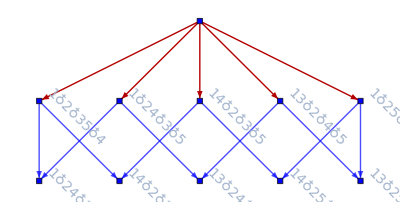

```mathematica
With[
{goodv={n1x2x35x4,n1x24x3x5,n1x25x3x4,n13x2x4x5,n14x2x3x5},
badv={n1x24x35,n13x24x5,n13x25x4,n14x2x35,n14x25x3}
},
With[
{good=EdgeList[Subgraph[g,DeleteDuplicates[Flatten[Table[VertexInComponent[g,k],{k,goodv}]]]]],
bad=DeleteDuplicates[Flatten[Table[VertexInComponent[g,k],{k,badv}]]]
},
Graph[Subgraph[g,DeleteDuplicates[Flatten[Table[VertexInComponent[g,k],{k,Join[goodv,badv]}]]]],
GraphHighlight->good,
VertexStyle->Table[v->Blue,{v,bad}],
ImageSize->Full,
EdgeStyle->Table[e->{Thick,Blue},{e,EdgeList[Subgraph[g,bad]]}],
VertexShapeFunction->"Square",
VertexLabels->Table[k->Rotate[Style[SymbolToLabel[k],14],-Pi/4],{k,Join[goodv,badv]}]
]
]
]
```

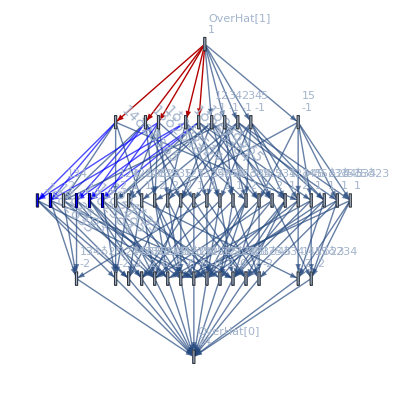

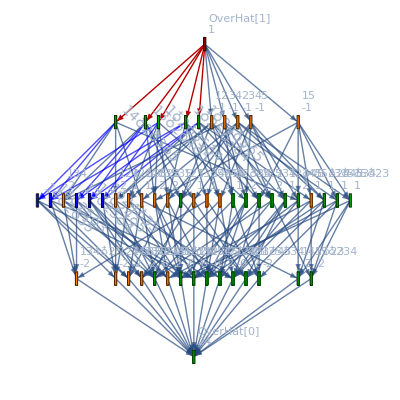

```mathematica
With[
{goodv={n1x2x35x4,n1x24x3x5,n1x25x3x4,n13x2x4x5,n14x2x3x5},
badv={n1x24x35,n13x24x5,n13x25x4,n14x2x35,n14x25x3}
},
With[
{good=EdgeList[Subgraph[g,DeleteDuplicates[Flatten[Table[VertexInComponent[g,k],{k,goodv}]]]]],
bad=DeleteDuplicates[Flatten[Table[VertexInComponent[g,k],{k,badv}]]]
},
Graph[g,
GraphHighlight->good,VertexStyle->Join[Table[v->Blue,{v,badv}],Table[ChangeSymbol[allGraphs5[k,"colofour"],"n"]->ColourForKey[allGraphs5,k],{k,Select[allGraphs5AtomKeys,!MemberQ[badv,ChangeSymbol[allGraphs5[#,"colofour"],"n"]]&]}]],
ImageSize->Full,
EdgeStyle->Table[e->{Thick,Blue},{e,EdgeList[Subgraph[g,bad]]}],
VertexShapeFunction->"Square",
VertexLabels->Table[k->Rotate[Style[SymbolToLabel[k],14],-Pi/4],{k,Join[goodv,badv]}],
AspectRatio->1
]
]
]
```

```mathematica
With[
{goodv={n1x2x34x5,n1x23x4x5,n15x5x3x4,n12x3x4x5,n15x2x3x4},
badv={n1x24x35,n13x24x5,n13x25x4,n14x2x35,n14x25x3}
},
Join[Table[v->Blue,{v,badv}],Table[ChangeSymbol[allGraphs5[k,"colofour"],"n"]->ColourForKey[allGraphs5,k],{k,Select[allGraphs5AtomKeys,!MemberQ[badv,ChangeSymbol[allGraphs5[#,"colofour"],"n"]]&]}]]
]
```

{n1x24x35→RGBColor[0, 0, 1],n13x24x5→RGBColor[0, 0, 1],n13x25x4→RGBColor[0, 0, 1],n14x2x35→RGBColor[0, 0, 1],n14x25x3→RGBColor[0, 0, 1],n1x2x3x4x5→RGBColor[Rational[2, 3], 0, 0],n1x2x3x45→RGBColor[1, 0.5, 0],n1x2x35x4→RGBColor[1, 0.5, 0],n1x2x34x5→RGBColor[1, 0.5, 0],n1x2x345→RGBColor[0, Rational[2, 3], 0],n1x25x3x4→RGBColor[1, 0.5, 0],n1x25x34→RGBColor[1, 0.5, 0],n1x24x3x5→RGBColor[1, 0.5, 0],n1x245x3→RGBColor[1, 0.5, 0],n1x23x4x5→RGBColor[1, 0.5, 0],n1x23x45→RGBColor[0, Rational[2, 3], 0],n1x235x4→RGBColor[1, 0.5, 0],n1x234x5→RGBColor[0, Rational[2, 3], 0],n1x2345→RGBColor[0, Rational[2, 3], 0],n15x2x3x4→RGBColor[1, 0.5, 0],n15x2x34→RGBColor[0, Rational[2, 3], 0],n15x24x3→RGBColor[1, 0.5, 0],n15x23x4→RGBColor[0, Rational[2, 3], 0],n15x234→RGBColor[0, Rational[2, 3], 0],n14x2x3x5→RGBColor[1, 0.5, 0],n14x23x5→RGBColor[1, 0.5, 0],n14x235→RGBColor[1, 0.5, 0],n145x2x3→RGBColor[0, Rational[2, 3], 0],n145x23→RGBColor[0, Rational[2, 3], 0],n13x2x4x5→RGBColor[1, 0.5, 0],n13x2x45→RGBColor[1, 0.5, 0],n13x245→RGBColor[1, 0.5, 0],n135x2x4→RGBColor[1, 0.5, 0],n135x24→RGBColor[1, 0.5, 0],n134x2x5→RGBColor[1, 0.5, 0],n134x25→RGBColor[1, 0.5, 0],n1345x2→RGBColor[0, Rational[2, 3], 0],n12x3x4x5→RGBColor[1, 0.5, 0],n12x3x45→RGBColor[0, Rational[2, 3], 0],n12x35x4→RGBColor[1, 0.5, 0],n12x34x5→RGBColor[0, Rational[2, 3], 0],n12x345→RGBColor[0, Rational[2, 3], 0],n125x3x4→RGBColor[0, Rational[2, 3], 0],n125x34→RGBColor[0, Rational[2, 3], 0],n124x3x5→RGBColor[1, 0.5, 0],n124x35→RGBColor[1, 0.5, 0],n1245x3→RGBColor[0, Rational[2, 3], 0],n123x4x5→RGBColor[0, Rational[2, 3], 0],n123x45→RGBColor[0, Rational[2, 3], 0],n1235x4→RGBColor[0, Rational[2, 3], 0],n1234x5→RGBColor[0, Rational[2, 3], 0],n12345→RGBColor[0, Rational[2, 3], 0]}

```mathematica
Keys[allGraphs6[0]]
```

{signature,matrix,graph,vertexsets,vertices,edges,relations,links,parents,children,comp,compwhy,colofour,colortable,colofourrealnull}

```mathematica
Tally[Table[allGraphs6[k,"comp"],{k,allGraphs6AtomKeys}]]
```

{{Equal,16},{GreaterEqual,151},{Greater,36}}

## Definitions can be found in D:\Users\alfredo\Google\Math\20171122 Plantri 8 renumbered.nb

```mathematica
formula8=FindFullFormula[pl8Ter];Put[formula8,"d:\\Saved\\formula8.m"]
```

$Aborted[]

```mathematica
FindFullFormula
```

```mathematica
Put[EdgeList[pl8Ter],"d:\\Saved\\pl8Ter.m"]
```

```mathematica
Put[AdjacencyMatrix[pl8Ter],"d:\\Saved\\pl8TerAdj.m"]
```

```mathematica
Put[Normal[IncidenceMatrix[pl8Ter]],"d:\\Saved\\pl8TerInc.m"]
```

```mathematica
Length[plantri]
```

100000

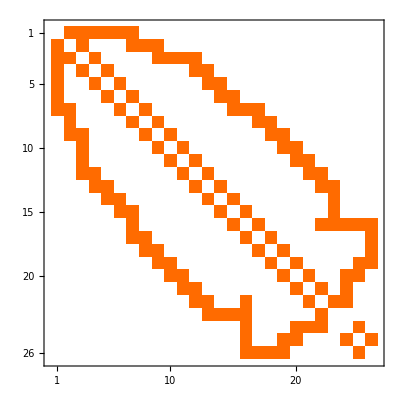
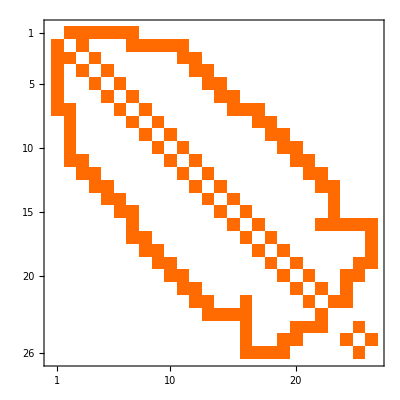
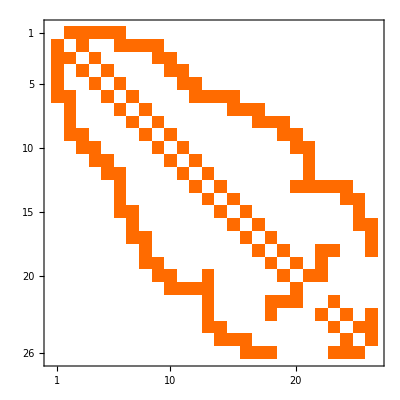
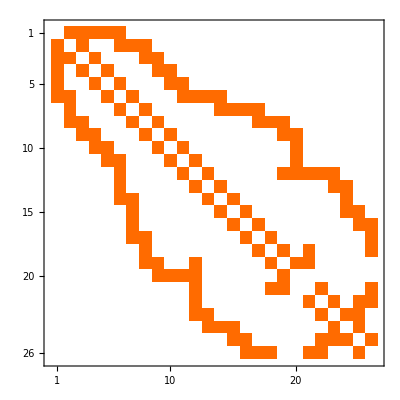
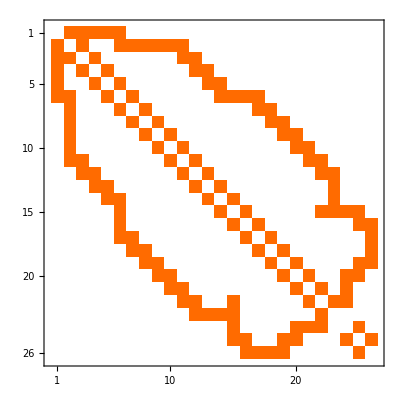
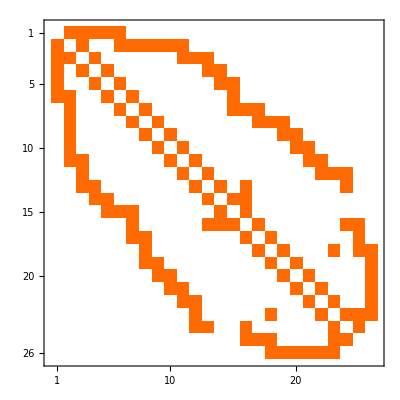
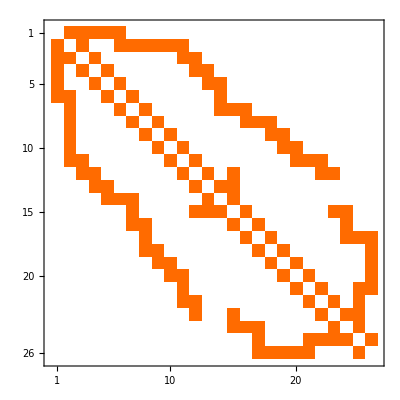
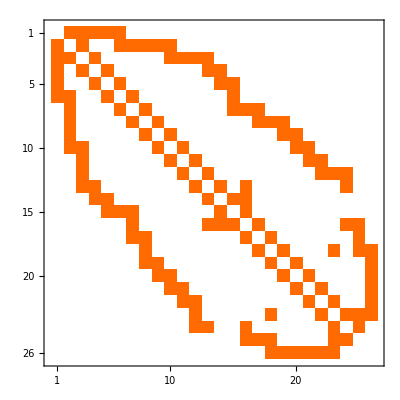

```mathematica
Table[MatrixPlot[Normal[AdjacencyMatrix[Graph[plantri[[k]]]]]],{k,Length[plantri]-10,Length[plantri]}]
```

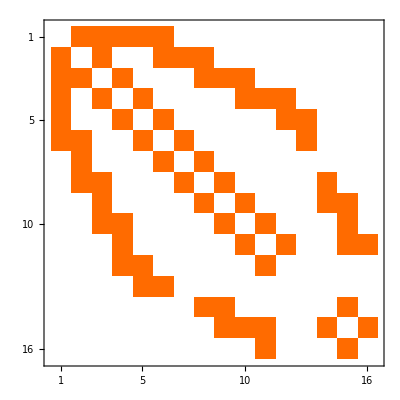

```mathematica
MatrixPlot[Normal[AdjacencyMatrix[pl8Ter]]]
```